```mathematica
dividedDiff[nodes_,values_] := (
If[ Length[nodes] == 1,
values[[1]],
(dividedDiff[  nodes[[2;;Length[nodes]]],values[[2;;Length[nodes]]]     ]  -  
dividedDiff[    nodes[[1;;Length[nodes]-1]],values[[1;;Length[nodes]-1 ]]      ])/
( nodes[[Length[nodes]]]-nodes[[1]] )

]

)
```

```mathematica
Newton[n_,x0_,h_,f_] := (
nodes = Table[x0+i*h,{i,0,n}];
values = f/.x->nodes;
poly = 0;
product = 1;
For[i=1,i≤Length[nodes],i++,
poly+=dividedDiff[nodes[[1;;i]],values[[1;;i]]]*product;
product *= x-nodes[[i]]
];
poly //Expand


)


p[x_] = Newton[4,1,1,1/(25+x^2)]
```

260447/6569225+(483 x)/525538-(321 x^2)/128180+(1113 x^3)/2627690-(613 x^4)/26276900

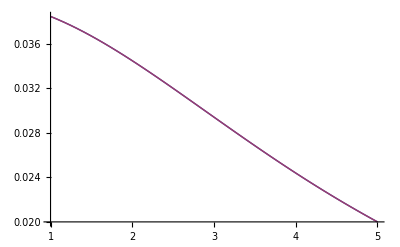

```mathematica
Plot[{p[x],1/(25+x^2)},{x,1,5}]
```